# Generic Natario warp drive and deflector shield

## Geometric quantities

```mathematica
ClearAll[coordsU];
coordsU={t,x,y,z};

ClearAll[vU];
vU={vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]};

ClearAll[gUU];
gUU=α[t,x,y,z]^(-2){
{-1,-vU[[1]],-vU[[2]],-vU[[3]]},
{-vU[[1]],α[t,x,y,z]^2-vU[[1]]vU[[1]],-vU[[1]]vU[[2]],-vU[[1]]vU[[3]]},
{-vU[[2]],-vU[[2]]vU[[1]],α[t,x,y,z]^2-vU[[2]]vU[[2]],-vU[[2]]vU[[3]]},
{-vU[[3]],-vU[[3]]vU[[1]],-vU[[3]]vU[[2]],α[t,x,y,z]^2-vU[[3]]vU[[3]]}
}//FullSimplify;

gLL=FullSimplify[Inverse[gUU]];

ClearAll[nU,nL];
nU=Join[{1/α[t,x,y,z]},vU/α[t,x,y,z]];
nL=FullSimplify[ParallelTable[Sum[gLL[[a,b]]nU[[b]],{b,1,4}],{a,1,4}]];
```

```mathematica
ClearAll[Γ];
Γ=ParallelTable[
FullSimplify[
(1/2)*Sum[
(gUU[[i,s]])*(D[gLL[[s,j]],coordsU[[k]] ]+D[gLL[[s,k]],coordsU[[j]] ]-D[gLL[[j,k]],coordsU[[s]] ]),
{s,1,4}
]
],
{i,1,4},
{j,1,4},
{k,1,4}
] ;
```

```mathematica
ClearAll[RiemannLLLL];
RiemannLLLL=ParallelTable[
FullSimplify[
D[Γ[[i,j,l]],coordsU[[k]] ]-D[Γ[[i,j,k]],coordsU[[l]] ]+Sum[
Γ[[s,j,l]] Γ[[i,k,s]]-Γ[[s,j,k]] Γ[[i,l,s]],
{s,1,4}
]
],
{i,1,4},
{j,1,4},
{k,1,4},
{l,1,4}
];

ClearAll[RicciLL];
RicciLL=FullSimplify[ParallelTable[Sum[RiemannLLLL[[i,j,i,l]],{i,1,4}],{j,1,4},{l,1,4}] ];

ClearAll[RicciScalar];
RicciScalar=FullSimplify[Sum[gUU[[i,j]]RicciLL[[i,j]],{i,1,4},{j,1,4}] ];

ClearAll[EinsteinLL];
EinsteinLL=FullSimplify[RicciLL-(1/2)RicciScalar*gLL];
```

```mathematica
ClearAll[KLL];
KLL=Table[
1/(2α[t,x,y,z])(D[gLL[[1,2;;4]][[j]],coordsU[[2;;4]][[i]]]+D[gLL[[1,2;;4]][[i]],coordsU[[2;;4]][[j]]]),
{i,1,3},
{j,1,3}
]//FullSimplify
```

{{-(vx^(0,1,0,0)[t,x,y,z])/α[t,x,y,z],-(vx^(0,0,1,0)[t,x,y,z]+vy^(0,1,0,0)[t,x,y,z])/(2 α[t,x,y,z]),-(vx^(0,0,0,1)[t,x,y,z]+vz^(0,1,0,0)[t,x,y,z])/(2 α[t,x,y,z])},{-(vx^(0,0,1,0)[t,x,y,z]+vy^(0,1,0,0)[t,x,y,z])/(2 α[t,x,y,z]),-(vy^(0,0,1,0)[t,x,y,z])/α[t,x,y,z],-(vy^(0,0,0,1)[t,x,y,z]+vz^(0,0,1,0)[t,x,y,z])/(2 α[t,x,y,z])},{-(vx^(0,0,0,1)[t,x,y,z]+vz^(0,1,0,0)[t,x,y,z])/(2 α[t,x,y,z]),-(vy^(0,0,0,1)[t,x,y,z]+vz^(0,0,1,0)[t,x,y,z])/(2 α[t,x,y,z]),-(vz^(0,0,0,1)[t,x,y,z])/α[t,x,y,z]}}

The Eulerian observer is a solution of the geodesic equation, if the lapse is 1

```mathematica
nU
```

{1/α[t,x,y,z],vx[t,x,y,z]/α[t,x,y,z],vy[t,x,y,z]/α[t,x,y,z],vz[t,x,y,z]/α[t,x,y,z]}

```mathematica
nL
```

{-α[t,x,y,z],0,0,0}

```mathematica
FullSimplify[
Table[
Sum[nU[[b]](D[nL[[b]],coordsU[[1]]]-Sum[Γ[[i,b,a]]nL[[i]],{i,1,4}]),{a,1,4},{b,1,4}],{c,1,4}
]
]
```

{(α^(0,0,0,1)[t,x,y,z]+α^(0,0,1,0)[t,x,y,z]+α^(0,1,0,0)[t,x,y,z]-3 α^(1,0,0,0)[t,x,y,z])/α[t,x,y,z],(α^(0,0,0,1)[t,x,y,z]+α^(0,0,1,0)[t,x,y,z]+α^(0,1,0,0)[t,x,y,z]-3 α^(1,0,0,0)[t,x,y,z])/α[t,x,y,z],(α^(0,0,0,1)[t,x,y,z]+α^(0,0,1,0)[t,x,y,z]+α^(0,1,0,0)[t,x,y,z]-3 α^(1,0,0,0)[t,x,y,z])/α[t,x,y,z],(α^(0,0,0,1)[t,x,y,z]+α^(0,0,1,0)[t,x,y,z]+α^(0,1,0,0)[t,x,y,z]-3 α^(1,0,0,0)[t,x,y,z])/α[t,x,y,z]}

```mathematica
ClearAll[EnergyDensity];
EnergyDensity=FullSimplify[1/(8π)Sum[EinsteinLL[[a,b]]*nU[[a]]nU[[b]],{a,1,4},{b,1,4}]]
```

-1/(32 π α[t,x,y,z]^2)((vy^(0,0,0,1)[t,x,y,z]+vz^(0,0,1,0)[t,x,y,z])^2-4 vy^(0,0,1,0)[t,x,y,z] vx^(0,1,0,0)[t,x,y,z]-4 vz^(0,0,0,1)[t,x,y,z] (vy^(0,0,1,0)[t,x,y,z]+vx^(0,1,0,0)[t,x,y,z])+(vx^(0,0,1,0)[t,x,y,z]+vy^(0,1,0,0)[t,x,y,z])^2+(vx^(0,0,0,1)[t,x,y,z]+vz^(0,1,0,0)[t,x,y,z])^2)

## Particle Hamiltonian

```mathematica
ClearAll[pL];
pL={pt,px,py,pz};

ClearAll[H];
H=FullSimplify[1/2Sum[gUU[[a,b]]pL[[a]]pL[[b]],{a,1,4},{b,1,4}]];

ClearAll[dHdpL];
dHdpL=FullSimplify[Table[D[H,pL[[i]]],{i,1,4}]];

ClearAll[dHdqU];
dHdqU=FullSimplify[Table[D[H,coordsU[[i]]],{i,1,4}]];

ClearAll[NormCons];
NormCons=Collect[Sum[gUU[[a,b]]pL[[a]]pL[[b]],{a,1,4},{b,1,4}]-δ,pt,FullSimplify];
```

## Transition functions

### Sharp transition

```mathematica
(*https://www.j-raedler.de/2010/10/smooth-transition-between-functions-with-tanh*)
(*https://en.wikipedia.org/wiki/Non-analytic_smooth_function#Smooth_transition_functions*)
ClearAll[SNAf,SNAg,SNAh];
SNAf[x_]:=Piecewise[{{Exp[-1/x],x>0},{0,x<=0}}];
SNAg[x_]:=SNAf[x]/(SNAf[x]+SNAf[1-x]);
SNAh[xa_,xb_,x_]:=SNAg[(x-xa)/(xb-xa)];

ClearAll[CInfTransition];
CInfTransition[x_,a_,xa_,b_,xb_]:=b*SNAh[xa,xb,x]+(1-SNAh[xa,xb,x])a;
CInfTransition[x_,y0_,x0_,Δx_]=FullSimplify[
CInfTransition[x,y0,x0,0,x0+Δx],
{
x∈Reals,
y0∈Reals,
x0∈Reals,
Δx∈Reals,
x>=0,
Δx>0
}
]
```

Piecewise[{{y0/(1+ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx)))), x>x0&&x<x0+Δx}, {0, x>x0}, {y0, True}}]

```mathematica
FullSimplify[
Derivative[1,0,0,0][CInfTransition][x,y0,x0,Δx],
{
x∈Reals,
y0∈Reals,
x0∈Reals,
Δx∈Reals,
x>=0,
Δx>0
}
]
```

Piecewise[{{-(ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx))) y0 Δx (1/(x-x0)^2+1/(-x+x0+Δx)^2))/((1+ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx))))^2), x>x0&&x<x0+Δx}, {0, True}}]

This transformation is necessary, otherwise the exponentials blow up when computing this numerically

```mathematica
ExpToTrig[-(ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx))) y0 Δx (1/(x-x0)^2+1/(-x+x0+Δx)^2))/((1+ⅇ^(Δx (1/(-x+x0)+1/(-x+x0+Δx))))^2)]//FullSimplify
```

-(y0 Δx (2 (x-x0)^2+2 (-x+x0) Δx+Δx^2) Sech[1/2 Δx (1/(-x+x0)+1/(-x+x0+Δx))]^2)/(4 (x-x0)^2 (-x+x0+Δx)^2)

```mathematica
FullSimplify[
Derivative[2,0,0,0][CInfTransition][x,y0,x0,Δx],
{
x∈Reals,
y0∈Reals,
x0∈Reals,
Δx∈Reals,
x>=0,
Δx>0
}
]
```

### Alcubierre transition

```mathematica
ClearAll[AlcubierreTransition]
AlcubierreTransition[σ_,R_,r_]:=(Tanh[σ(r+R)]-Tanh[σ(r-R)])/(2Tanh[σ*R]);
```

```mathematica
ClearAll[alc,dalc];
FullSimplify[Derivative[0,0,1][AlcubierreTransition][σ,R,x],{σ∈Reals,R∈Reals,x∈Reals,σ>0,R>0,x>=0}]
```

1/2 σ Coth[R σ] (-Sech[(-R+x) σ]^2+Sech[(R+x) σ]^2)

## Coordinate transformations for the Natario Drive

```mathematica
ClearAll[X];
X={2u*f[r]*Cos[θ],-u(2f[r]+r*f'[r])Sin[θ],0};

(* Sanity check:Does the original Natario functions have zero divergence in spherical coordinates? *)
Print["Div[X] == 0? ",FullSimplify[Div[X,{r,θ,ϕ},"Spherical"]==0]];

ClearAll[SphericalToCartesian];
SphericalToCartesian={
r*Sin[θ]Cos[ϕ],
r*Sin[θ]Sin[ϕ],
r*Cos[θ]
};

ClearAll[SphericalToCartesianRules];
SphericalToCartesianRules={
r->Sqrt[(x-u*t)^2+y^2+z^2],
θ->ArcCos[z/Sqrt[(x-u*t)^2+y^2+z^2]],
ϕ->ArcTan[(x-u*t),y]
};

ClearAll[XCartesian];
XCartesian=FullSimplify[
Table[Sum[X[[i]]D[SphericalToCartesian[[j]],{r,θ,ϕ}[[i]]],{i,1,3}],{j,1,3}]//.SphericalToCartesianRules,
{x∈Reals,y∈Reals,z∈Reals}
]
```

Div[X] == 0? True

{(u (t u-x) z √(1-z^2/((-t u+x)^2+y^2+z^2)) (2 (-1+√((-t u+x)^2+y^2+z^2)) f[√((-t u+x)^2+y^2+z^2)]+((-t u+x)^2+y^2+z^2) f'[√((-t u+x)^2+y^2+z^2)]))/(√((-t u+x)^2+y^2) √((-t u+x)^2+y^2+z^2)),-(u y z √(1-z^2/((-t u+x)^2+y^2+z^2)) (2 (-1+√((-t u+x)^2+y^2+z^2)) f[√((-t u+x)^2+y^2+z^2)]+((-t u+x)^2+y^2+z^2) f'[√((-t u+x)^2+y^2+z^2)]))/(√((-t u+x)^2+y^2) √((-t u+x)^2+y^2+z^2)),(2 u (z^2+((-t u+x)^2+y^2) √((-t u+x)^2+y^2+z^2)) f[√((-t u+x)^2+y^2+z^2)])/((-t u+x)^2+y^2+z^2)+u ((-t u+x)^2+y^2) f'[√((-t u+x)^2+y^2+z^2)]}

```mathematica
ClearAll[XCartesianReduced];
XCartesianReduced=FullSimplify[
XCartesian//.{(x-u*t)^2->r[t,x,y,z]^2-y^2-z^2},
{r[t,x,y,z]>=0}
]
```

{(u (t u-x) z (2 f[r[t,x,y,z]] (-1+r[t,x,y,z])+r[t,x,y,z]^2 f'[r[t,x,y,z]]))/r[t,x,y,z]^2,u y z (-(2 f[r[t,x,y,z]] (-1+r[t,x,y,z]))/r[t,x,y,z]^2-f'[r[t,x,y,z]]),(2 u f[r[t,x,y,z]] (z^2-z^2 r[t,x,y,z]+r[t,x,y,z]^3))/r[t,x,y,z]^2+u (-z^2+r[t,x,y,z]^2) f'[r[t,x,y,z]]}

Alternative Divergence free function:

```mathematica
FullSimplify[
Div[{
-2*y*z*f[r[t,x,y,z]],
(x-u*t)z*f[r[t,x,y,z]],
(x-u*t)y*f[r[t,x,y,z]]
},{x,y,z}]//.{
Derivative[0,1,0,0][r][t,x,y,z]->(x-u*t)/r[t,x,y,z],
Derivative[0,0,1,0][r][t,x,y,z]->y/r[t,x,y,z],
Derivative[0,0,0,1][r][t,x,y,z]->z/r[t,x,y,z]
}
]
```

0

## Code strings

### Propper formating of Power

```mathematica
Unprotect[Power];
Format[Power[E,a_],CForm]:=(exp[a]);
Format[Power[a_,1/2],CForm]:=(sqrt[a]);
Format[Power[a_,-1/2],CForm]:=(1/sqrt[a]);
Format[Power[a_,3/2],CForm]:=(a*sqrt[a]);
Format[Power[a_,2],CForm]:=(HoldForm[a*a]);
Format[Power[a_,-1],CForm]:=(HoldForm[1/(a)]);
Format[Power[a_,-2],CForm]:=(HoldForm[1/((a)*(a))]);
Format[Power[a_,b_],CForm]:=(powi[a,b])/;b∈Integers;
Format[Power[a_,b_],CForm]:=(powf[a,b]);
Protect[Power];
```

### Hamilton’s equations RHS

```mathematica
ClearAll[rules];
rules={
vx[t,x,y,z]->lvx,
vy[t,x,y,z]->lvy,
vz[t,x,y,z]->lvz,

D[vx[t,x,y,z],t]->dvxdt,
D[vx[t,x,y,z],x]->dvxdx,
D[vx[t,x,y,z],y]->dvxdy,
D[vx[t,x,y,z],z]->dvxdz,

D[vy[t,x,y,z],t]->dvydt,
D[vy[t,x,y,z],x]->dvydx,
D[vy[t,x,y,z],y]->dvydy,
D[vy[t,x,y,z],z]->dvydz,

D[vz[t,x,y,z],t]->dvzdt,
D[vz[t,x,y,z],x]->dvzdx,
D[vz[t,x,y,z],y]->dvzdy,
D[vz[t,x,y,z],z]->dvzdz,

α[t,x,y,z]->lalp,

D[α[t,x,y,z],t]->dalpdt,
D[α[t,x,y,z],x]->dalpdx,
D[α[t,x,y,z],y]->dalpdy,
D[α[t,x,y,z],z]->dalpdz
};

Print["let dhdpt = ",ToString[dHdpL[[1]]//.rules,CForm],";"]
Print["let dhdpx = ",ToString[dHdpL[[2]]//.rules,CForm],";"]
Print["let dhdpy = ",ToString[dHdpL[[3]]//.rules,CForm],";"]
Print["let dhdpz = ",ToString[dHdpL[[4]]//.rules,CForm],";"]

Print["let dhdqt = ",ToString[FullSimplify[dHdqU[[1]]//.rules],CForm],";"]
Print["let dhdqx = ",ToString[FullSimplify[dHdqU[[2]]//.rules],CForm],";"]
Print["let dhdqy = ",ToString[FullSimplify[dHdqU[[3]]//.rules],CForm],";"]
Print["let dhdqz = ",ToString[FullSimplify[dHdqU[[4]]//.rules],CForm],";"]

ClearAll[rules];
```

let dhdpt = -((pt + lvx*px + lvy*py + lvz*pz)/(lalp*lalp));

let dhdpx = px - (lvx*(pt + lvx*px + lvy*py + lvz*pz))/(lalp*lalp);

let dhdpy = py - (lvy*(pt + lvx*px + lvy*py + lvz*pz))/(lalp*lalp);

let dhdpz = pz - (lvz*(pt + lvx*px + lvy*py + lvz*pz))/(lalp*lalp);

let dhdqt = ((pt + lvx*px + lvy*py + lvz*pz)*(-(lalp*(dvxdt*px + dvydt*py + dvzdt*pz)) + dalpdt*(pt + lvx*px + lvy*py + lvz*pz)))/powi(lalp,3);

let dhdqx = ((pt + lvx*px + lvy*py + lvz*pz)*(-(lalp*(dvxdx*px + dvydx*py + dvzdx*pz)) + dalpdx*(pt + lvx*px + lvy*py + lvz*pz)))/powi(lalp,3);

let dhdqy = ((pt + lvx*px + lvy*py + lvz*pz)*(-(lalp*(dvxdy*px + dvydy*py + dvzdy*pz)) + dalpdy*(pt + lvx*px + lvy*py + lvz*pz)))/powi(lalp,3);

let dhdqz = ((pt + lvx*px + lvy*py + lvz*pz)*(-(lalp*(dvxdz*px + dvydz*py + dvzdz*pz)) + dalpdz*(pt + lvx*px + lvy*py + lvz*pz)))/powi(lalp,3);

### Normalization of pt

```mathematica
ClearAll[rules];
rules={
vx[t,x,y,z]->lvx,
vy[t,x,y,z]->lvy,
vz[t,x,y,z]->lvz,

α[t,x,y,z]->lalp
};

NormCons
Print["let a = ",ToString[Coefficient[NormCons,pt^2]//.rules,CForm],";"];
Print["let b = ",ToString[FullSimplify[Coefficient[NormCons,pt]]//.rules,CForm],";"];
Print["let c = ",ToString[FullSimplify[(NormCons//.pt->0)]//.rules,CForm],";"];

ClearAll[rules];
```

px^2+py^2+pz^2-δ-pt^2/α[t,x,y,z]^2-(2 pt (px vx[t,x,y,z]+py vy[t,x,y,z]+pz vz[t,x,y,z]))/α[t,x,y,z]^2-(px vx[t,x,y,z]+py vy[t,x,y,z]+pz vz[t,x,y,z])^2/α[t,x,y,z]^2

let a = -(1/(lalp*lalp));

let b = (-2*(lvx*px + lvy*py + lvz*pz))/(lalp*lalp);

let c = px*px + py*py + pz*pz - ((lvx*px + lvy*py + lvz*pz)*(lvx*px + lvy*py + lvz*pz))/(lalp*lalp) - δ;

### Radius functions and derivatives

```mathematica
ClearAll[strRules];
strRules={
"u"->"self.u",
"sqrt"->"f64::sqrt",
"epsilon"->"self.epsilon"
};

ClearAll[r];
r=Sqrt[(x-u*t)^2+y^2+z^2+epsilon];

Print["r = ",StringReplace[ToString[r,CForm],strRules]]
Print["d_r_dt = ",StringReplace[ToString[FullSimplify[D[r,t]],CForm],strRules]]
Print["d_r_dx = ",StringReplace[ToString[FullSimplify[D[r,x]],CForm],strRules]]
Print["d_r_dy = ",StringReplace[ToString[FullSimplify[D[r,y]],CForm],strRules]]
Print["d_r_dz = ",StringReplace[ToString[FullSimplify[D[r,z]],CForm],strRules]]

ClearAll[r];
ClearAll[strRules];
```

r = f64::sqrt(self.epsilon + (-(t*self.u) + x)*(-(t*self.u) + x) + y*y + z*z)

d_r_dt = (self.u*(t*self.u - x))/f64::sqrt(self.epsilon + (-(t*self.u) + x)*(-(t*self.u) + x) + y*y + z*z)

d_r_dx = (-(t*self.u) + x)/f64::sqrt(self.epsilon + (-(t*self.u) + x)*(-(t*self.u) + x) + y*y + z*z)

d_r_dy = y/f64::sqrt(self.epsilon + (-(t*self.u) + x)*(-(t*self.u) + x) + y*y + z*z)

d_r_dz = z/f64::sqrt(self.epsilon + (-(t*self.u) + x)*(-(t*self.u) + x) + y*y + z*z)

```mathematica
ClearAll[strRules];
strRules={
"u"->"self.u",
"sqrt"->"f64::sqrt",
"epsilon"->"self.epsilon"
};

ClearAll[r];

r=y/Sqrt[y^2+z^2+epsilon];

Print["r = ",StringReplace[ToString[r,CForm],strRules]]
Print["d_rho_y_dt = ",StringReplace[ToString[FullSimplify[D[r,t]],CForm],strRules]]
Print["d_rho_y_dx = ",StringReplace[ToString[FullSimplify[D[r,x]],CForm],strRules]]
Print["d_rho_y_dy = ",StringReplace[ToString[FullSimplify[D[r,y]],CForm],strRules]]
Print["d_rho_y_dz = ",StringReplace[ToString[FullSimplify[D[r,z]],CForm],strRules]]

ClearAll[r];
ClearAll[strRules];
```

r = y/f64::sqrt(self.epsilon + y*y + z*z)

d_rho_y_dt = 0

d_rho_y_dx = 0

d_rho_y_dy = (self.epsilon + z*z)/((self.epsilon + y*y + z*z)*f64::sqrt(self.epsilon + y*y + z*z))

d_rho_y_dz = -((y*z)/((self.epsilon + y*y + z*z)*f64::sqrt(self.epsilon + y*y + z*z)))

```mathematica
ClearAll[strRules];
strRules={
"u"->"self.u",
"sqrt"->"f64::sqrt",
"epsilon"->"self.epsilon"
};

ClearAll[r];

r=z/Sqrt[y^2+z^2+epsilon];

Print["r = ",StringReplace[ToString[r,CForm],strRules]]
Print["d_rho_z_dt = ",StringReplace[ToString[FullSimplify[D[r,t]],CForm],strRules]]
Print["d_rho_z_dx = ",StringReplace[ToString[FullSimplify[D[r,x]],CForm],strRules]]
Print["d_rho_z_dy = ",StringReplace[ToString[FullSimplify[D[r,y]],CForm],strRules]]
Print["d_rho_z_dz = ",StringReplace[ToString[FullSimplify[D[r,z]],CForm],strRules]]

ClearAll[r];
ClearAll[strRules];
```

r = z/f64::sqrt(self.epsilon + y*y + z*z)

d_rho_z_dt = 0

d_rho_z_dx = 0

d_rho_z_dy = -((y*z)/((self.epsilon + y*y + z*z)*f64::sqrt(self.epsilon + y*y + z*z)))

d_rho_z_dz = (self.epsilon + y*y)/((self.epsilon + y*y + z*z)*f64::sqrt(self.epsilon + y*y + z*z))

### Natario Velocities

```mathematica
Print["vx = ",StringReplace[ToString[XCartesianReduced[[1]]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
Print["vz = ",StringReplace[ToString[XCartesianReduced[[2]]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
Print["vy = ",StringReplace[ToString[XCartesianReduced[[3]]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
```

vx = (self.bubble_speed*(2*lf*(-1 + lr) + dfdr*(lr*lr))*(self.bubble_speed*t - x)*z)/(lr*lr)

vz = self.bubble_speed*(-dfdr - (2*lf*(-1 + lr))/(lr*lr))*y*z

vy = self.bubble_speed*dfdr*(lr*lr - z*z) + (2*self.bubble_speed*lf*(f64::powi(lr,3) + z*z - lr*(z*z)))/(lr*lr)

```mathematica
Print["d_vx_dt = ",StringReplace[ToString[D[XCartesianReduced[[1]],t]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
Print["d_vx_dx = ",StringReplace[ToString[D[XCartesianReduced[[1]],x]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
Print["d_vx_dy = ",StringReplace[ToString[D[XCartesianReduced[[1]],y]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
Print["d_vx_dz = ",StringReplace[ToString[D[XCartesianReduced[[1]],z]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
```

d_vx_dt = (self.bubble_speed*self.bubble_speed*(2*lf*(-1 + lr) + dfdr*(lr*lr))*z)/(lr*lr) - (2*self.bubble_speed*drdt*(2*lf*(-1 + lr) + dfdr*(lr*lr))*(self.bubble_speed*t - x)*z)/f64::powi(lr,3) + (self.bubble_speed*(2*drdt*lf + 2*dfdr*drdt*(-1 + lr) + 2*dfdr*drdt*lr + d2fdr2*drdt*(lr*lr))*(self.bubble_speed*t - x)*z)/(lr*lr)

d_vx_dx = -((self.bubble_speed*(2*lf*(-1 + lr) + dfdr*(lr*lr))*z)/(lr*lr)) - (2*self.bubble_speed*drdx*(2*lf*(-1 + lr) + dfdr*(lr*lr))*(self.bubble_speed*t - x)*z)/f64::powi(lr,3) + (self.bubble_speed*(2*drdx*lf + 2*dfdr*drdx*(-1 + lr) + 2*dfdr*drdx*lr + d2fdr2*drdx*(lr*lr))*(self.bubble_speed*t - x)*z)/(lr*lr)

d_vx_dy = (-2*self.bubble_speed*drdy*(2*lf*(-1 + lr) + dfdr*(lr*lr))*(self.bubble_speed*t - x)*z)/f64::powi(lr,3) + (self.bubble_speed*(2*drdy*lf + 2*dfdr*drdy*(-1 + lr) + 2*dfdr*drdy*lr + d2fdr2*drdy*(lr*lr))*(self.bubble_speed*t - x)*z)/(lr*lr)

d_vx_dz = (self.bubble_speed*(2*lf*(-1 + lr) + dfdr*(lr*lr))*(self.bubble_speed*t - x))/(lr*lr) - (2*self.bubble_speed*drdz*(2*lf*(-1 + lr) + dfdr*(lr*lr))*(self.bubble_speed*t - x)*z)/f64::powi(lr,3) + (self.bubble_speed*(2*drdz*lf + 2*dfdr*drdz*(-1 + lr) + 2*dfdr*drdz*lr + d2fdr2*drdz*(lr*lr))*(self.bubble_speed*t - x)*z)/(lr*lr)

```mathematica
Print["d_vy_dt = ",StringReplace[ToString[D[XCartesianReduced[[2]],t]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
Print["d_vy_dx = ",StringReplace[ToString[D[XCartesianReduced[[2]],x]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
Print["d_vy_dy = ",StringReplace[ToString[D[XCartesianReduced[[2]],y]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
Print["d_vy_dz = ",StringReplace[ToString[D[XCartesianReduced[[2]],z]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
```

d_vy_dt = self.bubble_speed*(-(d2fdr2*drdt) + (4*drdt*lf*(-1 + lr))/f64::powi(lr,3) - (2*drdt*lf)/(lr*lr) - (2*dfdr*drdt*(-1 + lr))/(lr*lr))*y*z

d_vy_dx = self.bubble_speed*(-(d2fdr2*drdx) + (4*drdx*lf*(-1 + lr))/f64::powi(lr,3) - (2*drdx*lf)/(lr*lr) - (2*dfdr*drdx*(-1 + lr))/(lr*lr))*y*z

d_vy_dy = self.bubble_speed*(-dfdr - (2*lf*(-1 + lr))/(lr*lr))*z + self.bubble_speed*(-(d2fdr2*drdy) + (4*drdy*lf*(-1 + lr))/f64::powi(lr,3) - (2*drdy*lf)/(lr*lr) - (2*dfdr*drdy*(-1 + lr))/(lr*lr))*y*z

d_vy_dz = self.bubble_speed*(-dfdr - (2*lf*(-1 + lr))/(lr*lr))*y + self.bubble_speed*(-(d2fdr2*drdz) + (4*drdz*lf*(-1 + lr))/f64::powi(lr,3) - (2*drdz*lf)/(lr*lr) - (2*dfdr*drdz*(-1 + lr))/(lr*lr))*y*z

```mathematica
Print["d_vz_dt = ",StringReplace[ToString[D[XCartesianReduced[[3]],t]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
Print["d_vz_dx = ",StringReplace[ToString[D[XCartesianReduced[[3]],x]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
Print["d_vz_dy = ",StringReplace[ToString[D[XCartesianReduced[[3]],y]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
Print["d_vz_dz = ",StringReplace[ToString[D[XCartesianReduced[[3]],z]//.fRules//.u->bubbleSpeed,CForm],rustRules]]
```

d_vz_dt = 2*self.bubble_speed*dfdr*drdt*lr + self.bubble_speed*d2fdr2*drdt*(lr*lr - z*z) + (2*self.bubble_speed*lf*(3*drdt*(lr*lr) - drdt*(z*z)))/(lr*lr) - (4*self.bubble_speed*drdt*lf*(f64::powi(lr,3) + z*z - lr*(z*z)))/f64::powi(lr,3) + (2*self.bubble_speed*dfdr*drdt*(f64::powi(lr,3) + z*z - lr*(z*z)))/(lr*lr)

d_vz_dx = 2*self.bubble_speed*dfdr*drdx*lr + self.bubble_speed*d2fdr2*drdx*(lr*lr - z*z) + (2*self.bubble_speed*lf*(3*drdx*(lr*lr) - drdx*(z*z)))/(lr*lr) - (4*self.bubble_speed*drdx*lf*(f64::powi(lr,3) + z*z - lr*(z*z)))/f64::powi(lr,3) + (2*self.bubble_speed*dfdr*drdx*(f64::powi(lr,3) + z*z - lr*(z*z)))/(lr*lr)

d_vz_dy = 2*self.bubble_speed*dfdr*drdy*lr + self.bubble_speed*d2fdr2*drdy*(lr*lr - z*z) + (2*self.bubble_speed*lf*(3*drdy*(lr*lr) - drdy*(z*z)))/(lr*lr) - (4*self.bubble_speed*drdy*lf*(f64::powi(lr,3) + z*z - lr*(z*z)))/f64::powi(lr,3) + (2*self.bubble_speed*dfdr*drdy*(f64::powi(lr,3) + z*z - lr*(z*z)))/(lr*lr)

d_vz_dz = self.bubble_speed*dfdr*(2*drdz*lr - 2*z) + self.bubble_speed*d2fdr2*drdz*(lr*lr - z*z) + (2*self.bubble_speed*lf*(3*drdz*(lr*lr) + 2*z - 2*lr*z - drdz*(z*z)))/(lr*lr) - (4*self.bubble_speed*drdz*lf*(f64::powi(lr,3) + z*z - lr*(z*z)))/f64::powi(lr,3) + (2*self.bubble_speed*dfdr*drdz*(f64::powi(lr,3) + z*z - lr*(z*z)))/(lr*lr)

### Our velocities

```mathematica
ClearAll[OurVelocities]
OurVelocities={
w[t]*f[r[t,x,y,z]],
w[t]rhoX[y,z]*f[r[t,x,y,z]],
0
};
```

```mathematica
Print["d_vx_dt = ",StringReplace[ToString[D[OurVelocities[[1]],t]//.fRules,CForm],rustRules]]
Print["d_vx_dx = ",StringReplace[ToString[D[OurVelocities[[1]],x]//.fRules,CForm],rustRules]]
Print["d_vx_dy = ",StringReplace[ToString[D[OurVelocities[[1]],y]//.fRules,CForm],rustRules]]
Print["d_vx_dz = ",StringReplace[ToString[D[OurVelocities[[1]],z]//.fRules,CForm],rustRules]]
```

d_vx_dt = dwdt*lf + dfdr*drdt*wt

d_vx_dx = dfdr*drdx*wt

d_vx_dy = dfdr*drdy*wt

d_vx_dz = dfdr*drdz*wt

```mathematica
Print["d_vy_dt = ",StringReplace[ToString[D[OurVelocities[[2]],t]//.fRules,CForm],rustRules]]
Print["d_vy_dx = ",StringReplace[ToString[D[OurVelocities[[2]],x]//.fRules,CForm],rustRules]]
Print["d_vy_dy = ",StringReplace[ToString[D[OurVelocities[[2]],y]//.fRules,CForm],rustRules]]
Print["d_vy_dz = ",StringReplace[ToString[D[OurVelocities[[2]],z]//.fRules,CForm],rustRules]]
```

d_vy_dt = dfdr*drdt*k*rho(x,y)

d_vy_dx = dfdr*drdx*k*rho(x,y) + k*lf*Derivative(1,0)(rho)(x,y)

d_vy_dy = dfdr*drdy*k*rho(x,y) + k*lf*Derivative(0,1)(rho)(x,y)

d_vy_dz = dfdr*drdz*k*rho(x,y)

```mathematica
Print["d_vz_dt = ",StringReplace[ToString[D[OurVelocities[[3]],t]//.fRules,CForm],rustRules]]
Print["d_vz_dx = ",StringReplace[ToString[D[OurVelocities[[3]],x]//.fRules,CForm],rustRules]]
Print["d_vz_dy = ",StringReplace[ToString[D[OurVelocities[[3]],y]//.fRules,CForm],rustRules]]
Print["d_vz_dz = ",StringReplace[ToString[D[OurVelocities[[3]],z]//.fRules,CForm],rustRules]]
```

d_vz_dt = 0

d_vz_dx = 0

d_vz_dy = 0

d_vz_dz = 0

## Sharp Alcubierre drive with deflection energy density

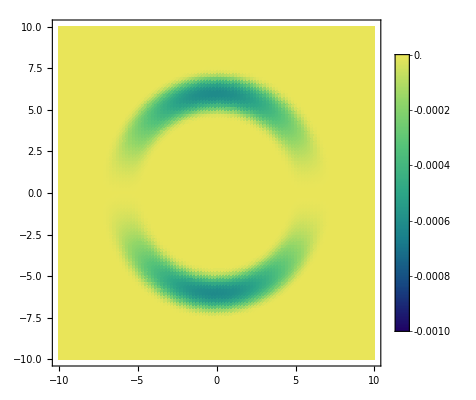

```mathematica
ClearAll[ρ];
ρ=y/Sqrt[y^2+z^2];

ClearAll[f];
f=FullSimplify[TopHat[σ,R,r],{σ∈Reals,R∈Reals,x∈Reals,σ>0,R>0,r>=0}];

ClearAll[r];
r=Sqrt[(x-v*t)^2+y^2+z^2];

ClearAll[vx,vy,vz];
vx[t_,x_,y_,z_]=v*f;
vy[t_,x_,y_,z_]=k*ρ*f;
vz[t_,x_,y_,z_]=0;

ClearAll[σ,R,k,v];
σ=4;
R=4;
k=1/100;
v=1/2;

ClearAll[slice];
slice=Simplify[EnergyDensity//.{t->0,z->0},{x∈Reals,y∈Reals}];

ClearAll[xyRange,zRange];
xyRange=R+σ+2;
zRange={-1/1000,0};

DensityPlot[
slice,
{x,-xyRange,xyRange},
{y,-xyRange,xyRange},

PlotPoints->100,

ColorFunctionScaling->False,
ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,zRange]]&),

PlotRange->{Automatic,Automatic,zRange},

PlotLegends->BarLegend[{Automatic,zRange}],

Exclusions->None
]

ClearAll[xyRange,zRange];
ClearAll[slice];
ClearAll[σ,R,k,v];
ClearAll[vx,vy,vz];
ClearAll[r];
ClearAll[f];
ClearAll[ρ];
```